```mathematica
Rep = Import["/home/gutiloluis/61Monograph/mas-gillespie/h_rep.dat", {"Data",All,1}];
Unrep = Import["/home/gutiloluis/61Monograph/mas-gillespie/h_unrep.dat", {"Data",All,1}];
```

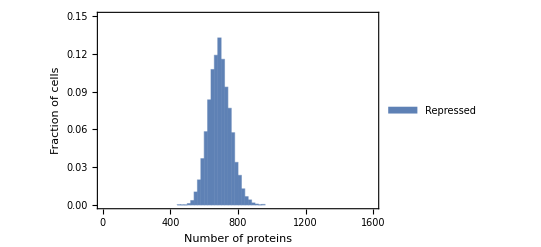

```mathematica
optGen = {Axes->None,Frame->True,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[30,FontFamily->"Palatino Linotype",Black],FrameLabel->{Text[Style["Number of proteins"]],Text[Style["Fraction of cells"]]},PlotRange->{{0,1600},{0,0.15}}};
imSize = {ImageSize->1000};
optHrep = {ChartStyle->ColorData[97,"ColorList"][[1]]};
legendHrep={ChartLegends->Placed[SwatchLegend[{"Repressed"},LegendMarkerSize->{20},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",4},Spacings->0.2],{0.87,0.88}]};
hrep=Histogram[Rep,30,"Probability",Evaluate[optHrep],Evaluate[optGen],Evaluate[legendHrep]]
```

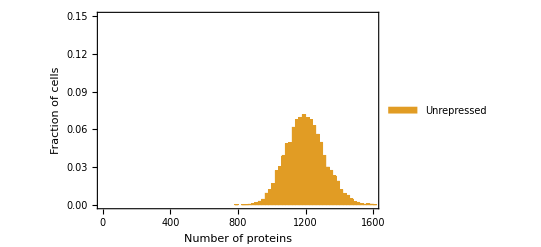

```mathematica
optHunrep = {ChartStyle->ColorData[97,"ColorList"][[2]]};
legendHunrep={ChartLegends->Placed[SwatchLegend[{"Unrepressed"},LegendMarkerSize->{20},LabelStyle->{FontFamily->"Palatino Linotype",20},LegendLayout->{"Row",4},Spacings->0.2],{0.8835,0.82}]};
hunrep=Histogram[Unrep,45,"Probability",Evaluate[optHunrep],Evaluate[optGen],Evaluate[legendHunrep]]
```

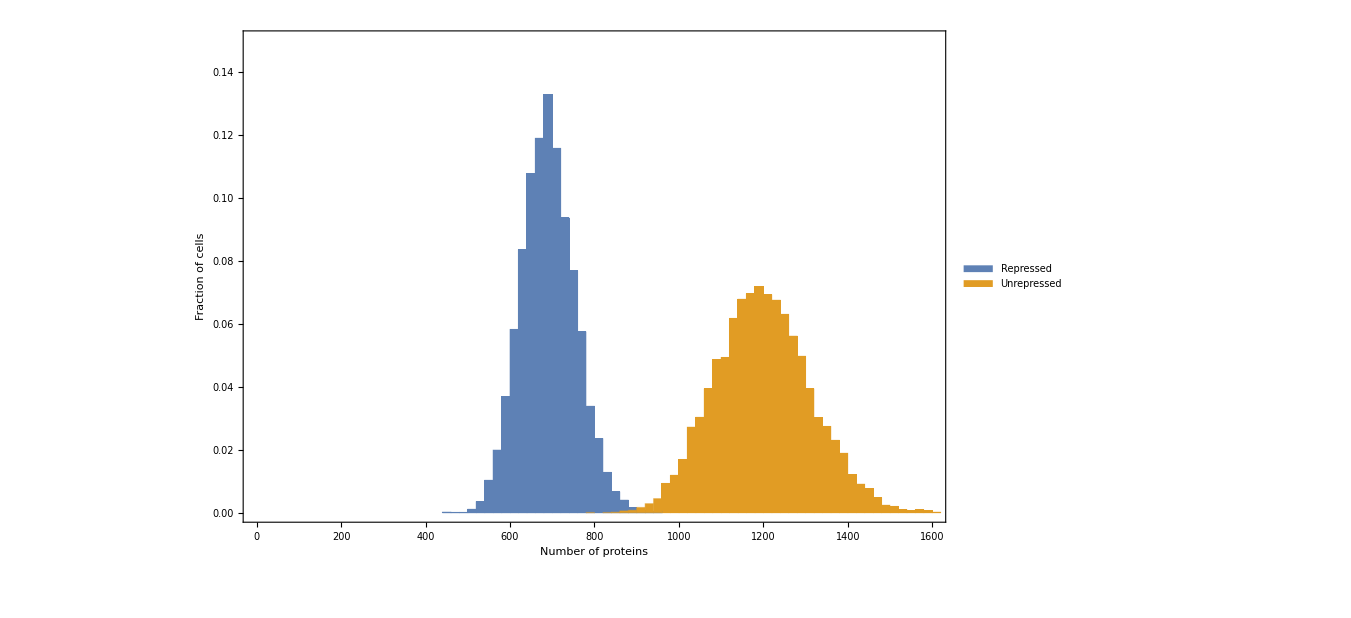

```mathematica
Gh=Show[hrep,hunrep,Evaluate[imSize]]
Export["/home/gutiloluis/61Monograph/images/mas-hist.png",Gh];
```

{{x→Function[{t},(ⅇ^(-gr t) (-1+ⅇ^(gr t)) kr)/gr],y→Function[{t},(ⅇ^(-gp t-gr t) (-ⅇ^(gp t) gp+ⅇ^(gp t+gr t) gp+ⅇ^(gr t) gr-ⅇ^(gp t+gr t) gr) kp kr)/(gp (gp-gr) gr)]}}

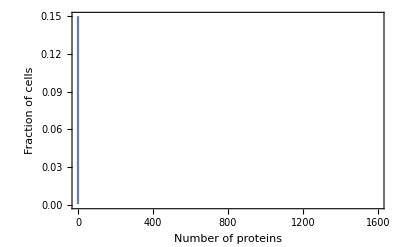

```mathematica
DSolve[{x'[t]==kr-gr*x[t],y'[t]==kp*x[t]-gp*y[t],x[0]==0,y[0]==0},{x,y},t]
```